# Ferromagnetic Hysteresis with Stress

## Front matter

### Setup the notebook

Reset the environment

```mathematica
Remove["Global`*"]
```

#### Load the initialize cells from Github

```mathematica
Get[NotebookDirectory[]<>"InitWorksheet.wl"];
```

#### Unit definition

```mathematica
$UnitSystem="Metric"
```

Metric

#### Commonly used substitutions

```mathematica
subFmtPub= {μo->Subscript[μ, o],μr->Subscript[μ, r],μri->Subscript[μ, r,i],μrd->Subscript[μ, r,d],μrxi->Subscript[μ, rx,i],
Ar->A,do->Subscript[d, o],
ℛspi->Subscript[ℛ, sp,i],ℛsprecti->Subscript[ℛ, sprect,i],ℛspcirci->Subscript[ℛ, spcirc,i],ℛopengapi->Subscript[ℛ, opengap,i],
𝒫spi->Subscript[𝒫, sp,i],𝒫sprecti->Subscript[𝒫, sprect,i],𝒫spcirci->Subscript[𝒫, spcirc,i],𝒫opengapi->Subscript[𝒫, br],
𝒫br->Subscript[𝒫, br],𝒫d->Subscript[𝒫, d],𝒫s->Subscript[𝒫, s],𝒫t->Subscript[𝒫, t],𝒫tall ->Subscript[𝒫, t,all],
𝒫0d->Subscript[𝒫, 0,d],𝒫0s->Subscript[𝒫, 0,s],
𝒫1d->Subscript[𝒫, 1,d],𝒫1s->Subscript[𝒫, 1,s],
𝒫2d->Subscript[𝒫, 2,d],𝒫2s->Subscript[𝒫, 2,s],
𝒫1->Subscript[𝒫, 1],𝒫2->Subscript[𝒫, 2],𝒫sd->Subscript[𝒫, s,d],𝒫3->Subscript[𝒫, 3],
ℛcore->Subscript[ℛ, core],ℛsd->Subscript[ℛ, sd], ℛ2->Subscript[ℛ, 2],
ℛgaps->Subscript[ℛ, gap,s], ℛt->Subscript[ℛ, t],ℛ3->Subscript[ℛ, 3],ℛgapd->Subscript[ℛ, gap,d],
𝒫core->Subscript[𝒫, core],
gu->Subscript[g, u],
Vs->Subscript[V, s],Id->Subscript[Ii, d],
vout->Subscript[v, output], v3->Subscript[v, 3],v4->Subscript[v, 4], v1->Subscript[v, 1], v2->Subscript[v, 2],
id->Subscript[i, d],z1->Subscript[z, 1],z2->Subscript[z, 2],z3->Subscript[z, 3],z4->Subscript[z, 4],
𝒫gapd->Subscript[𝒫, gap,d],𝒫gaps->Subscript[𝒫, gap,s],
𝒫breddy->Subscript[𝒫, br,eddy],𝒫deddy->Subscript[𝒫, d,eddy],𝒫seddy->Subscript[𝒫, s,eddy],
λs->Subscript[λ, s],c11->Subscript[c, 11],c12->Subscript[c, 12],
Heff->Subscript[H, eff],σ0->Subscript[σ, 0],Hσ->Subscript[H, σ],
γ1->Subscript[γ, 1],γ2->Subscript[γ, 2],
Man->Subscript[M, an],DMan->Subscript[DM, an],kb->Subscript[k, b]}
```

{μo→μ_o,μr→μ_r,μri→μ_(r,i),μrd→μ_(r,d),μrxi→μ_(rx,i),Ar→A,do→d_o,ℛspi→ℛ_(sp,i),ℛsprecti→ℛ_(sprect,i),ℛspcirci→ℛ_(spcirc,i),ℛopengapi→ℛ_(opengap,i),𝒫spi→𝒫_(sp,i),𝒫sprecti→𝒫_(sprect,i),𝒫spcirci→𝒫_(spcirc,i),𝒫opengapi→𝒫_br,𝒫br→𝒫_br,𝒫d→𝒫_d,𝒫s→𝒫_s,𝒫t→𝒫_t,𝒫tall→𝒫_(t,all),𝒫0d→𝒫_(0,d),𝒫0s→𝒫_(0,s),𝒫1d→𝒫_(1,d),𝒫1s→𝒫_(1,s),𝒫2d→𝒫_(2,d),𝒫2s→𝒫_(2,s),𝒫1→𝒫_1,𝒫2→𝒫_2,𝒫sd→𝒫_(s,d),𝒫3→𝒫_3,ℛcore→ℛ_core,ℛsd→ℛ_sd,ℛ2→ℛ_2,ℛgaps→ℛ_(gap,s),ℛt→ℛ_t,ℛ3→ℛ_3,ℛgapd→ℛ_(gap,d),𝒫core→𝒫_core,gu→g_u,Vs→V_s,Id→Ii_d,vout→v_output,v3→v_3,v4→v_4,v1→v_1,v2→v_2,id→i_d,z1→z_1,z2→z_2,z3→z_3,z4→z_4,𝒫gapd→𝒫_(gap,d),𝒫gaps→𝒫_(gap,s),𝒫breddy→𝒫_(br,eddy),𝒫deddy→𝒫_(d,eddy),𝒫seddy→𝒫_(s,eddy),λs→λ_s,c11→c_11,c12→c_12,Heff→H_eff,σ0→σ_0,Hσ→H_σ,γ1→γ_1,γ2→γ_2,Man→M_an,DMan→DM_an,kb→k_b}

```mathematica
subCode={μo->muo,μr->mur,μri->muri,μrd->murd,μrxi->murxi,
𝒫br->Pbr,𝒫d->Pd,𝒫s->Ps,𝒫t->Pt,𝒫3->P3,
ρ->rho, ω->omega,δ->delta,
𝒫0s->P0s,𝒫1s->P1s,𝒫2s->P2s,𝒫sd->Psd,𝒫eq->Peq,𝒫core->Pcore,𝒫->P,
𝒫breddy->Pbreddy,𝒫deddy->Pdeddy,𝒫seddy->Pseddy}
```

{μo→muo,μr→mur,μri→muri,μrd→murd,μrxi→murxi,𝒫br→Pbr,𝒫d→Pd,𝒫s→Ps,𝒫t→Pt,𝒫3→P3,ρ→rho,ω→omega,δ→delta,𝒫0s→P0s,𝒫1s→P1s,𝒫2s→P2s,𝒫sd→Psd,𝒫eq→Peq,𝒫core→Pcore,𝒫→P,𝒫breddy→Pbreddy,𝒫deddy→Pdeddy,𝒫seddy→Pseddy}

#### Assumptions and nomenclature

Assumptions about which parameters are reals:

```mathematica
$Assumptions={R1∈Reals,R2∈Reals,R3∈Reals, ℙ∈Reals,  ℙ12∈Reals, ℙ3∈Reals, ω ∈Reals, ϵ ∈Reals}
```

{R1∈ℝ,R2∈ℝ,R3∈ℝ,ℙ∈ℝ,ℙ12∈ℝ,ℙ3∈ℝ,ω∈ℝ,ϵ∈ℝ}

LaPlace nomenclature

```mathematica
LaplaceSub = {vs-> Vs,vd-> Vd,vsc-> Vsc,
i1-> I1,i2-> I2,i3-> I3,
is->Is, id->Id, it->It}
```

{vs→Vs,vd→Vd,vsc→Vsc,i1→I1,i2→I2,i3→I3,is→Is,id→Id,it→It}

## Problem setup

### Reference:

[1] 	D. Jiles and D. Atherton, “Ferromagnetic hysteresis,” in IEEE Transactions on Magnetics, vol. 19, no. 5, pp. 2183-2185, September 1983, doi: 10.1109/TMAG.1983.1062594.
[2]  	Jiles, D. C., and D. L. Atherton. “Theory of Ferromagnetic Hysteresis.” Journal of Magnetism and Magnetic Materials, vol. 61, nos. 1–2, 1986, pp. 48–60.
[3]  	Jiles, D. C. “Theory of the Magnetomechanical Effect.” Journal of Physics D: Applied Physics, vol. 28, 1995, pp. 1537–1546.

### Diagrams and drawings

-Graphics-

-Graphics-

### Nomenclature:

a 		Anhysteretic magnetization shape parameter, A/m
B 		Magnetic flux density, Tesla
H 		Internal magnetic field, A/m
H_σ 		Internal magnetic field due to stress, A/m
k 		Anhysteretic factor describing pinning energy, A/m
M 		Bulk magnetization, A/m
M_s		Saturation magnetization,  A/m
α 		mean field parameter, -
θ 		Angle between stress and magnetic field, radians
μ_o 		Permeability of a vacuum, H/m
ν 		Poisson’s ratio, -
σ 		Stress, Pa
σ_0 		Applied stress, Pa

### Common equations

#### Effective internal magnetic field

Begin with the fundamental equation for the effective field, Eq (3) in [1]:

```mathematica
eqnEffField = Heff==H + α M +Hσ;
eqnEffField/.subFmtPub
```

H_eff==H+M α+H_σ

#### Internal magnetic field due to stress

Jiles makes a good point about how the magnetic field may be co-axial to the applied stress, Eq (4):

```mathematica
eqnStressMagField = σ == σ0*(Cos[θ]^2-ν Sin[θ]^2);
HoldForm[Evaluate[eqnStressMagField]]/.subFmtPub
```

σ==σ_0 (Cos[θ]^2-ν Sin[θ]^2)

From Eq. (5) in [3] Jiles defines the internal field due to stress:

```mathematica
eqnMagFieldDueToStress = Hσ==(3/2)*(σ/μo)* dλdMσ;
eqnMagFieldDueToStress/.subFmtPub
```

H_σ==(3 dλdMσ σ)/(2 μ_o)

#### Internal magnetic field due to stress (cont.)

Re-write using the overall applied stress to get the final form of Eq. (5) in [3]:

```mathematica
eqnMagFieldDueToStress=eqnMagFieldDueToStress/.{eqnStressMagField/.Equal->Rule};
eqnMagFieldDueToStress/.subFmtPub
```

H_σ==(3 dλdMσ (Cos[θ]^2-ν Sin[θ]^2) σ_0)/(2 μ_o)

Following [1] and including terms up to 2:

```mathematica
eqnLambda = λ==γ1 M^2+γ2 M^4;
HoldForm[Evaluate[eqnLambda]]/.subFmtPub
```

λ==M^2 γ_1+M^4 γ_2

```mathematica
eqnLambdaDer = dλdMσ==D[eqnLambda[[2]],M]
```

dλdMσ==2 M γ1+4 M^3 γ2

Make the substitution and take the derivative:

```mathematica
eqnMagFieldDueToStress = eqnMagFieldDueToStress/.(eqnLambdaDer/.Equal->Rule);
eqnMagFieldDueToStress/.subFmtPub
```

H_σ==(3 (Cos[θ]^2-ν Sin[θ]^2) (2 M γ_1+4 M^3 γ_2) σ_0)/(2 μ_o)

#### Anhysteretic curve

Use the  expression for anhysteretic magnetization, Eq. (6) from [2]:

```mathematica
eqnAnHys = Man== Ms(Coth[Heff/a]-(a/Heff));
eqnAnHys/.subFmtPub
```

M_an==Ms (Coth[H_eff/a]-a/H_eff)

Where, in Eq. (1) of [3], Jiles describes a anhysteretic shape factor as:

```mathematica
eqnAnhShape = a==(kb T)/(μo M);
eqnAnhShape/.subFmtPub
```

a==(T k_b)/(M μ_o)

```mathematica
eqnAnHysMagneto = eqnAnHys/.{eqnEffField/.Equal->Rule};
eqnAnHysMagneto/.subFmtPub
```

M_an==Ms (Coth[(H+M α+H_σ)/a]-a/(H+M α+H_σ))

```mathematica
eqnAnHysMagnetoStress = eqnAnHysMagneto/.{eqnMagFieldDueToStress/.Equal->Rule};
eqnAnHysMagnetoStress/.subFmtPub
```

M_an==Ms (Coth[(H+M α+(3 (Cos[θ]^2-ν Sin[θ]^2) (2 M γ_1+4 M^3 γ_2) σ_0)/(2 μ_o))/a]-a/(H+M α+(3 (Cos[θ]^2-ν Sin[θ]^2) (2 M γ_1+4 M^3 γ_2) σ_0)/(2 μ_o)))

```mathematica
eqnAnHysMagnetoDMDH=DMan/DH==D[eqnAnHysMagneto[[2]],H];
eqnAnHysMagnetoDMDH/.subFmtPub
```

DM_an/DH==Ms (-Csch[(H+M α+H_σ)/a]^2/a+a/(H+M α+H_σ)^2)

#### Anhysteretic Taylor Series Expansion

Neither the expression for anhysteretic curve or its deriviative behave well around zero. The  most robust way to work around this is to use  a few terms from the Tayler series  expansion when the effective magnetic field, H_eff, is small.

Get the Maclaurin series

```mathematica
eqnAnHysSeries = Series[eqnAnHys[[2]],{Heff,0,4}]
```

(Ms Heff)/(3 a)-(Ms Heff^3)/(45 a^3)+O[Heff]^5

Convert the series to Horner form to help with execution

```mathematica
eqnAnHysHorner = HornerForm[Normal[eqnAnHysSeries]]
```

(15 a^2 Heff Ms-Heff^3 Ms)/(45 a^3)

Horner form to computer code

```mathematica
CForm[eqnAnHysHorner]
```

(15*Power(a,2)*Heff*Ms - Power(Heff,3)*Ms)/(45.*Power(a,3))

#### Hysteresis - WiP

The final expression for irreversible hysteresis, Eq. (19)  in [3]:

```mathematica
eqnJA = DM/DH==(1/(1+c))*(1/(δ k / μo ) - α(Man - M))*(Man-M)+(c/(1+c))*eqnAnHysMagnetoDMDH[[2]]
eqnJA/.subFmtPub
```

DM/DH==((-M+Man) (-((-M+Man) α)+μo/(k δ)))/(1+c)+(c Ms (a/(H+Hσ+M α)^2-Csch[(H+Hσ+M α)/a]^2/a))/(1+c)

DM/DH==(c Ms (-Csch[(H+M α+H_σ)/a]^2/a+a/(H+M α+H_σ)^2))/(1+c)+((-M+M_an) (-α (-M+M_an)+μ_o/(k δ)))/(1+c)

```mathematica
eqnJAIntegrated = M==Integrate[eqnJA[[2]],H]
```

M==(-(a c Ms)/(H+Hσ+M α)+H (-M+Man) (M α-Man α+μo/(k δ))+c Ms Coth[(H+Hσ+M α)/a])/(1+c)

## Validation at the origin - WiP

The computational code must branch around the singularity at the origin. This section establishes the bound for those tests:

```mathematica
dMsInput = Quantity[1.9, "Amperes"/"Meters"]; PrintMagField[dMsInput,Label->"M_s", Precision->9]
dMInput = Quantity[0.00, "Amperes"/"Meters"]; PrintMagField[dMInput,Label->"M", Precision->9]
daInput = Quantity[18, "Amperes"/"Meters"]; PrintMagField[daInput,Label->"a", Precision->9]
dαInput = 1.6*10^-3;PrintUnitless[dαInput, Label->"α", Precision->9]
dcInput = 0.2;PrintUnitless[dcInput, Label->"c", Precision->9]
dkInput = 400;PrintUnitless[dkInput, Label->"k", Precision->9]
dθInput = 0°; PrintAngle[dθInput, Label->"θ", Precision ->9]
dσ0Input = Quantity[00, "Megapascals"]; PrintPress[dσ0Input, Label->"θ_0", Precision->9]
μoInput = UnitConvert[Quantity["MagneticConstant"],"Henries"/"Meters"];  PrintPermeability[μoInput, Label->"μ_0", Precision->9]
```

M_s: 1.9 A/m (0.0238761042 Oe)

M: 0. A/m (0. Oe)

a: 18. A/m (0.226194671 Oe)

α: 0.001600000 (0.001600000)

c: 0.200000000 (0.200000000)

k: 400.000000000 (400.000000000)

θ: 0.000000000 ° (0.000000000 rad)

θ_0: 0. kPa (0. lbf/in^20. bar)

μ_0: 1.25663706×10^-6 H/m (3.19185814×10^-8 H/in)

### Define substitution rules

```mathematica
subFigOrigin= {Ms->dMsInput, a->daInput, d->dkInput,
α->dαInput, c->dcInput,
θ->dθInput, σ0->dσ0Input, μo->μoInput, M->dMInput};
subFigOrigin = Flatten[{subFigOrigin,  γ1->(dγ1Input/.subFigOrigin),  γ2->(dγ2Input/.subFigOrigin)}]
```

{Ms→1.9 A/m,a→18 A/m,d→400,α→0.0016,c→0.2,θ→0,σ0→0 MPa,μo→1.25663706×10^-6 H/m,M→0. A/m,γ1→dγ1Input,γ2→dγ2Input}

Calculate the anhysteretic value for this test point:

```mathematica
solAnHysMagneto= eqnAnHysMagnetoStress/.subFigOrigin;
solAnHysMagneto=solAnHysMagneto /.H -> Quantity[+1.0*10^-9, "Amperes"/"Meters"];
PrintMagField[solAnHysMagneto[[2]], Label->"M_an", Precision->19]
PrintUnitless[solAnHysMagneto[[2]]/dMsInput, Label->"M_an/M_s", Precision->19]
```

PrintMagField[(Coth[((0 m MPa/H) (dγ2Input (0. A^3/m^3)+dγ1Input (0. A/m))+1.×10^-9 A/m) (1/18 m/A)]+(-18 A/m)/((0 m MPa/H) (dγ2Input (0. A^3/m^3)+dγ1Input (0. A/m))+1.×10^-9 A/m)) (1.9 A/m),Label→M_an,Precision→19]

PrintUnitless[1. (Coth[((0 m MPa/H) (dγ2Input (0. A^3/m^3)+dγ1Input (0. A/m))+1.×10^-9 A/m) (1/18 m/A)]+(-18 A/m)/((0 m MPa/H) (dγ2Input (0. A^3/m^3)+dγ1Input (0. A/m))+1.×10^-9 A/m)),Label→M_an/M_s,Precision→19]

## Values from Figure 2 in [3]

### Define the values

```mathematica
dMsInput = Quantity[1.7*10^6, "Amperes"/"Meters"]; PrintMagField[dMsInput,Label->"M_s", Precision->9]
dMInput = Quantity[0.00, "Amperes"/"Meters"]; PrintMagField[dMInput,Label->"M", Precision->9]
daInput = Quantity[1000, "Amperes"/"Meters"]; PrintMagField[daInput,Label->"a", Precision->9]
dkInput = Quantity[1000, "Amperes"/"Meters"]; PrintMagField[dkInput,Label->"k", Precision->9]
dαInput = 1.0*10^-3;PrintUnitless[dαInput, Label->"α", Precision->9]
dcInput = 0.1;PrintUnitless[dcInput, Label->"c", Precision->9]
dθInput = 0°; PrintAngle[dθInput, Label->"θ", Precision ->9]
dγ1Input =Quantity[4.0*10^-18 - (2 * 10^-26)*QuantityMagnitude[UnitConvert[σ0, "Pascals"]],("Meters")^2/("Amperes")^2]  
dγ2Input =Quantity[2.0*10^-30 - (5 * 10^-39)*QuantityMagnitude[UnitConvert[σ0, "Pascals"]],("Meters")^4/("Amperes")^4]  
μoInput = UnitConvert[Quantity["MagneticConstant"],"Henries"/"Meters"];  PrintPermeability[μoInput, Label->"μ_0", Precision->9]
```

M_s: 1.7×10^6 A/m (21362.83 Oe)

M: 0. A/m (0. Oe)

a: 1000. A/m (12.5663706 Oe)

k: 1000. A/m (12.5663706 Oe)

α: 0.001000000 (0.001000000)

c: 0.100000000 (0.100000000)

θ: 0.000000000 ° (0.000000000 rad)

(4.×10^-18-QuantityMagnitude[UnitConvert[σ0,Pascals]]/50000000000000000000000000) m^2/A^2

(2.×10^-30-QuantityMagnitude[UnitConvert[σ0,Pascals]]/200000000000000000000000000000000000000) m^4/A^4

μ_0: 1.25663706×10^-6 H/m (3.19185814×10^-8 H/in)

### Define substitution rules

```mathematica
subFig2= {Ms->dMsInput, a->daInput, c->dcInput,k->dkInput,
α->dαInput, θ->dθInput, μo->μoInput, M->dMInput};
```

Zero-stress

```mathematica
subStress000000 = σ0-> Quantity[00, "Megapascals"]; PrintPress[subStress000000[[2]], Label->"θ_0", Precision->9]
subFig2Stress000000 = Flatten[{subFig2, subStressNeg100, γ1->(dγ1Input/.subStress000000),  γ2->(dγ2Input/.subStress000000)}]
```

θ_0: 0. kPa (0. lbf/in^20. bar)

{Ms→1.7×10^6 A/m,a→1000 A/m,c→0.1,k→1000 A/m,α→0.001,θ→0,μo→1.25663706×10^-6 H/m,M→0. A/m,subStressNeg100,γ1→4.×10^-18 m^2/A^2,γ2→2.×10^-30 m^4/A^4}

Define substitutions for -100 MPa

```mathematica
subStressNeg100 = σ0-> Quantity[-100, "Megapascals"]; PrintPress[subStressNeg100[[2]], Label->"θ_0", Precision->9]
subFig2StressNeg100 = Flatten[{subFig2,subStressNeg100,  γ1->(dγ1Input/.subStressNeg100),  γ2->(dγ2Input/.subStressNeg100)}]
```

θ_0: -100000. kPa (-14503.7738 lbf/in^2-1000. bar)

{Ms→1.7×10^6 A/m,a→1000 A/m,c→0.1,k→1000 A/m,α→0.001,θ→0,μo→1.25663706×10^-6 H/m,M→0. A/m,σ0→-100 MPa,γ1→6.×10^-18 m^2/A^2,γ2→2.5×10^-30 m^4/A^4}

### Find the values for Figure 2

Make all substitutions, except for the stress values:

```mathematica
solAnHysMagneto= eqnAnHysMagnetoStress/.subFig2
solAnHysMagneto=solAnHysMagneto /.H -> Quantity[300, "Amperes"/"Meters"]
```

Man==(Coth[(1/1000 m/A) (H+0. A/m+σ0 (γ2 (0. A^3/m^3)+γ1 (0. A/m)) (1.19366207×10^6 m/H))]+(-1000 A/m)/(H+0. A/m+σ0 (γ2 (0. A^3/m^3)+γ1 (0. A/m)) (1.19366207×10^6 m/H))) (1.7×10^6 A/m)

Man==(Coth[(1/1000 m/A) (300. A/m+σ0 (γ2 (0. A^3/m^3)+γ1 (0. A/m)) (1.19366207×10^6 m/H))]+(-1000 A/m)/(300. A/m+σ0 (γ2 (0. A^3/m^3)+γ1 (0. A/m)) (1.19366207×10^6 m/H))) (1.7×10^6 A/m)

Substitute the test values and format for zero-stress conditions

```mathematica
solAnHysMagneto000000= solAnHysMagneto/.subFig2Stress000000
PrintMagField[solAnHysMagneto000000[[2]], Label->"M_an", Precision->19]
PrintUnitless[solAnHysMagneto000000[[2]]/dMsInput, Label->"M_an/M_s", Precision->19]
```

Man==168989. A/m

M_an: 168988.6648802935 A/m (2123.57419251151 Oe)

M_an/M_s: 0.0994050969884079000 (0.0994050969884079000)

### Plot values for Figure 2

#### Derive better form for plotting (Zero stress)

Build the anhysteretic expression from your symbolic equation

```mathematica
exprMan000000=(eqnAnHysMagnetoStress/. subFig2)[[2]];
exprMan000000= exprMan000000/.subFig2Stress000000;

(*Define the anhysteretic magnetization ratio M_an/M_s as a function of H*)
fManOverMs000000[H_]:=Evaluate[UnitConvert[(exprMan000000/dMsInput)/. H->H,1]];

(*Define the anhysteretic magnetization M_an as a function of H*)
fMan000000[H_]:=Evaluate[(exprMan000000/. H->H)];
```

Quick check at the point you already validated

```mathematica
PrintMagField[fMan000000[Quantity[300,"Amperes"/"Meters"]], Label->"M_an", Precision->19]
PrintUnitless[fManOverMs000000[Quantity[300,"Amperes"/"Meters"]], Label->"M_an/M_s", Precision->19]
```

M_an: 168988.6648802935 A/m (2123.57419251151 Oe)

M_an/M_s: 0.0994050969884079000 (0.0994050969884079000)

#### Derive better form for plotting (negative stress)

```mathematica
exprManNeg100=(eqnAnHysMagnetoStress/. subFig2)[[2]];
exprManNeg100= exprManNeg100/.subFig2StressNeg100;

(*Define the anhysteretic magnetization ratio M_an/M_s as a function of H*)
fManOverMsNeg100[H_]:=Evaluate[UnitConvert[(exprManNeg100/dMsInput)/. H->H,1]];

(*Define the anhysteretic magnetization M_an as a function of H*)
fManNeg100[H_]:=Evaluate[(exprManNeg100/. H->H)];
```

Quick check at the point you already validated

```mathematica
PrintMagField[fManNeg100[Quantity[300,"Amperes"/"Meters"]], Label->"M_an", Precision->19]
PrintUnitless[fManOverMsNeg100[Quantity[300,"Amperes"/"Meters"]], Label->"M_an/M_s", Precision->19]
```

M_an: 168988.6648802935 A/m (2123.57419251151 Oe)

M_an/M_s: 0.0994050969884079000 (0.0994050969884079000)

#### Format for the in-plot title

Handy-dandy formatting goodness

```mathematica
formatInsetText[a_,units_:"Amperes"/"Meters"]:=
Module[{val},
val=UnitConvert[a,units];
ToString[ScientificForm[
QuantityMagnitude[val],
4],
StandardForm]
]
```

Extract parameter values from your substitution set

```mathematica
dMsVal=dMsInput/. subFig2;
msText=formatInsetText[dMsVal];
```

```mathematica
daVal=a/. subFig2;
aText=formatInsetText[daVal];
```

```mathematica
dkVal=k/. subFig2;
kText=formatInsetText[dkVal];
```

```mathematica
dAlphaVal=α/. subFig2;
alphaText=ToString[ScientificForm[dAlphaVal,4],StandardForm];
```

```mathematica
dcVal=c/. subFig2;
cText=ToString[ScientificForm[dcVal,4],StandardForm];
```

Create the inset image

```mathematica
paramBox=Framed[
Style[
Grid[
{
{"Model Parameters",""},
{"Ms =",msText<> " A/m"},
{"a =",aText<> " A/m"},
{"k =",kText<> " A/m"},
{"α =",alphaText},
{"c =",cText}
},
Alignment->Left,
Spacings->{1,0.4}
],
12,
Black
],
Background->White,
FrameStyle->GrayLevel[0.7],
RoundingRadius->4
];
```

#### Generate the plot with normalized magnetic field

Generate hysteresis table

```mathematica
dVertScale = 1000;
tblAnhys=Table[{Quantity[h,"Amperes"/"Meters"],fMan000000[Quantity[h,"Amperes"/"Meters"]]/dVertScale},{h,-15000,15000,100.1}];
NumberForm[Take[tblAnhys,{69,70}]//TableForm,9]
```

-8193.2 A/m | -1492.51112 A/m
-8093.1 A/m | -1489.94484 A/m

#### Now with units of magnetic flux density

```mathematica
tblAnhysB={#1, UnitConvert[(#1 +#2*dVertScale)* μoInput, "Teslas"]}&@@@tblAnhys;
NumberForm[Take[tblAnhysB,{69,70}]//TableForm,9]
```

-8193.2 A/m | -1.88584067 T
-8093.1 A/m | -1.88248999 T

#### Create the plot to match Fig. (3)

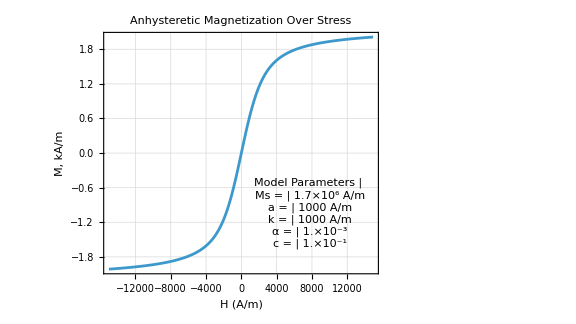

```mathematica
plotAnHystStressFig2 = ListLinePlot[
tblAnhysB,
Frame->True,GridLines->Automatic,
FrameLabel->{"H (A/m)","M, kA/m"},
PlotLabel->"Anhysteretic Magnetization Over Stress",
PlotRange->All,
AspectRatio->9/16,
Epilog->{Inset[paramBox,Scaled[{0.75,0.25}]]},
ImageSize->Large
]
```

#### Create the plot with units of bulk magnetization on the vertical axis

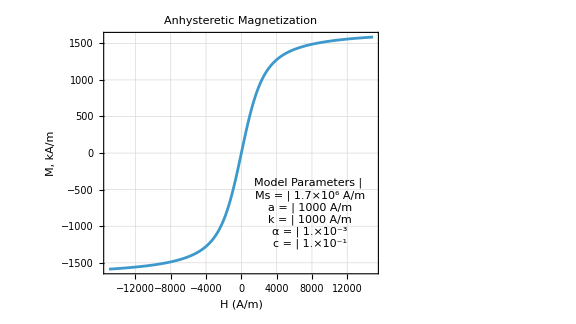

```mathematica
plotAnHystStressFig2M = ListLinePlot[
tblAnhys,
Frame->True,GridLines->Automatic,
FrameLabel->{"H (A/m)","M, kA/m"},
PlotLabel->"Anhysteretic Magnetization",
PlotRange->All,
AspectRatio->9/16,
Epilog->{Inset[paramBox,Scaled[{0.75,0.25}]]},
ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[] <>"Anhyst_Stress_Fig2_Mag.pdf",plotAnHystStressFig2M];
```

```mathematica
Clear[{tblAnhys, plotAnHystStressFig2, dVertScale, plotAnHystStressFig2M}]
```

#### Generate the plot with normalized magnetic field

Generate hysteresis table

```mathematica
tblAnhysNorm=Table[{h,fManOverMs[Quantity[h,"Amperes"/"Meters"]]},{h,-70000,70000,100.1}];
```

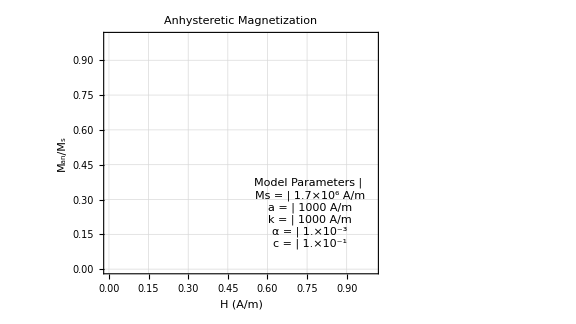

```mathematica
plotAnHystFig3Norm = ListLinePlot[
tblAnhysNorm,
Frame->True,GridLines->Automatic,
FrameLabel->{"H (A/m)","\!\(\*SubscriptBox[\(M\), \(an\)]\)/\!\(\*SubscriptBox[\(M\), \(s\)]\)"},
PlotLabel->"Anhysteretic Magnetization",
PlotRange->All,
AspectRatio->9/16,
Epilog->{Inset[paramBox,Scaled[{0.75,0.25}]]},
ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[] <>"Anhyst_Fig3_Norm.pdf",plotAnHystFig3Norm];
```

```mathematica
Clear[{tblAnhysNorm, plotAnHystFig3Norm}]
```

### Compare numerical and analytical derivatives

```mathematica
solAnHysMagnetoDMDH= eqnAnHysMagnetoDMDH/.subFig3;
solAnHysMagnetoDMDH=solAnHysMagnetoDMDH /.H -> Quantity[300, "Amperes"/"Meters"];
PrintUnitless[solAnHysMagnetoDMDH[[2]], Label->"dM_an/dH", Precision->19]
```

ReplaceAll::reps: {subFig3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

PrintUnitless[subFig3,Label→dM_an/dH,Precision→19]

```mathematica
(*Build the anhysteretic expression from your symbolic equation*)
exprDManDH=(eqnAnHysMagnetoDMDH/. subFig3)[[2]];

(*Define the anhysteretic magnetization M_an as a function of H*)
fDManDH[H_]:=Evaluate[(exprDManDH/. H->H)];
```

ReplaceAll::reps: {subFig3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
tblAnhysDmanDH=Table[{h,fDManDH[Quantity[h,"Amperes"/"Meters"]]},{h,-70000,70000,100.1}];
Take[tblAnhysDmanDH,{699,701}]//TableForm
```

-130.2 | subFig3
-30.1 | subFig3
70. | subFig3

```mathematica
plotAnHystDmanDH = ListLinePlot[
{tblAnhysDmanDH, tblAnhysNumDer},
Frame->True,GridLines->Automatic,
FrameLabel->{"H (A/m)","\!\(\*SubscriptBox[\(M\), \(an\)]\)/\!\(\*SubscriptBox[\(M\), \(s\)]\)"},
PlotLabel->"Derivative of Anhysteretic Magnetization with Respect to Internal Field",
PlotRange->All,
AspectRatio->9/16,
ImageSize->Large,
PlotLegends->{"Analytic dMan/dH","Numeric dMan/dH"}
]
```

ListLinePlot::lpn: {{{-70000.,subFig3},{-69899.9,subFig3},{-69799.8,subFig3},{-69699.7,subFig3},{-69599.6,subFig3},{-69499.5,subFig3},{-69399.4,subFig3},{-69299.3,subFig3},{-69199.2,subFig3},{-69099.1,subFig3},{-68999.,subFig3},{-68898.9,subFig3},{-68798.8,subFig3},{-68698.7,subFig3},{-68598.6,subFig3},{-68498.5,subFig3},{-68398.4,subFig3},{-68298.3,subFig3},{-68198.2,subFig3},«13»,{-66796.8,subFig3},{-66696.7,subFig3},{-66596.6,subFig3},{-66496.5,subFig3},{-66396.4,subFig3},{-66296.3,subFig3},{-66196.2,subFig3},{-66096.1,subFig3},{-65996.,subFig3},{-65895.9,subFig3},{-65795.8,subFig3},{-65695.7,subFig3},{-65595.6,subFig3},{-65495.5,subFig3},{-65395.4,subFig3},{-65295.3,subFig3},{-65195.2,subFig3},{-65095.1,subFig3},«1349»},{}} is not a list of numbers or pairs of numbers.

ListLinePlot[{{{-70000.,subFig3},{-69899.9,subFig3},{-69799.8,subFig3},{-69699.7,subFig3},{-69599.6,subFig3},{-69499.5,subFig3},{-69399.4,subFig3},{-69299.3,subFig3},{-69199.2,subFig3},{-69099.1,subFig3},{-68999.,subFig3},{-68898.9,subFig3},{-68798.8,subFig3},{-68698.7,subFig3},{-68598.6,subFig3},{-68498.5,subFig3},{-68398.4,subFig3},{-68298.3,subFig3},{-68198.2,subFig3},{-68098.1,subFig3},{-67998.,subFig3},{-67897.9,subFig3},{-67797.8,subFig3},{-67697.7,subFig3},{-67597.6,subFig3},{-67497.5,subFig3},{-67397.4,subFig3},{-67297.3,subFig3},{-67197.2,subFig3},{-67097.1,subFig3},{-66997.,subFig3},{-66896.9,subFig3},{-66796.8,subFig3},{-66696.7,subFig3},{-66596.6,subFig3},{-66496.5,subFig3},{-66396.4,subFig3},{-66296.3,subFig3},{-66196.2,subFig3},{-66096.1,subFig3},{-65996.,subFig3},{-65895.9,subFig3},{-65795.8,subFig3},{-65695.7,subFig3},{-65595.6,subFig3},{-65495.5,subFig3},{-65395.4,subFig3},{-65295.3,subFig3},{-65195.2,subFig3},{-65095.1,subFig3},{-64995.,subFig3},{-64894.9,subFig3},{-64794.8,subFig3},{-64694.7,subFig3},{-64594.6,subFig3},{-64494.5,subFig3},{-64394.4,subFig3},{-64294.3,subFig3},{-64194.2,subFig3},{-64094.1,subFig3},{-63994.,subFig3},{-63893.9,subFig3},{-63793.8,subFig3},{-63693.7,subFig3},{-63593.6,subFig3},{-63493.5,subFig3},{-63393.4,subFig3},{-63293.3,subFig3},{-63193.2,subFig3},{-63093.1,subFig3},{-62993.,subFig3},{-62892.9,subFig3},{-62792.8,subFig3},{-62692.7,subFig3},{-62592.6,subFig3},{-62492.5,subFig3},{-62392.4,subFig3},{-62292.3,subFig3},{-62192.2,subFig3},{-62092.1,subFig3},{-61992.,subFig3},{-61891.9,subFig3},{-61791.8,subFig3},{-61691.7,subFig3},{-61591.6,subFig3},{-61491.5,subFig3},{-61391.4,subFig3},{-61291.3,subFig3},{-61191.2,subFig3},{-61091.1,subFig3},{-60991.,subFig3},{-60890.9,subFig3},{-60790.8,subFig3},{-60690.7,subFig3},{-60590.6,subFig3},{-60490.5,subFig3},{-60390.4,subFig3},{-60290.3,subFig3},{-60190.2,subFig3},{-60090.1,subFig3},{-59990.,subFig3},{-59889.9,subFig3},{-59789.8,subFig3},{-59689.7,subFig3},{-59589.6,subFig3},{-59489.5,subFig3},{-59389.4,subFig3},{-59289.3,subFig3},{-59189.2,subFig3},{-59089.1,subFig3},{-58989.,subFig3},{-58888.9,subFig3},{-58788.8,subFig3},{-58688.7,subFig3},{-58588.6,subFig3},{-58488.5,subFig3},{-58388.4,subFig3},{-58288.3,subFig3},{-58188.2,subFig3},{-58088.1,subFig3},{-57988.,subFig3},{-57887.9,subFig3},{-57787.8,subFig3},{-57687.7,subFig3},{-57587.6,subFig3},{-57487.5,subFig3},{-57387.4,subFig3},{-57287.3,subFig3},{-57187.2,subFig3},{-57087.1,subFig3},{-56987.,subFig3},{-56886.9,subFig3},{-56786.8,subFig3},{-56686.7,subFig3},{-56586.6,subFig3},{-56486.5,subFig3},{-56386.4,subFig3},{-56286.3,subFig3},{-56186.2,subFig3},{-56086.1,subFig3},{-55986.,subFig3},{-55885.9,subFig3},{-55785.8,subFig3},{-55685.7,subFig3},{-55585.6,subFig3},{-55485.5,subFig3},{-55385.4,subFig3},{-55285.3,subFig3},{-55185.2,subFig3},{-55085.1,subFig3},{-54985.,subFig3},{-54884.9,subFig3},{-54784.8,subFig3},{-54684.7,subFig3},{-54584.6,subFig3},{-54484.5,subFig3},{-54384.4,subFig3},{-54284.3,subFig3},{-54184.2,subFig3},{-54084.1,subFig3},{-53984.,subFig3},{-53883.9,subFig3},{-53783.8,subFig3},{-53683.7,subFig3},{-53583.6,subFig3},{-53483.5,subFig3},{-53383.4,subFig3},{-53283.3,subFig3},{-53183.2,subFig3},{-53083.1,subFig3},{-52983.,subFig3},{-52882.9,subFig3},{-52782.8,subFig3},{-52682.7,subFig3},{-52582.6,subFig3},{-52482.5,subFig3},{-52382.4,subFig3},{-52282.3,subFig3},{-52182.2,subFig3},{-52082.1,subFig3},{-51982.,subFig3},{-51881.9,subFig3},{-51781.8,subFig3},{-51681.7,subFig3},{-51581.6,subFig3},{-51481.5,subFig3},{-51381.4,subFig3},{-51281.3,subFig3},{-51181.2,subFig3},{-51081.1,subFig3},{-50981.,subFig3},{-50880.9,subFig3},{-50780.8,subFig3},{-50680.7,subFig3},{-50580.6,subFig3},{-50480.5,subFig3},{-50380.4,subFig3},{-50280.3,subFig3},{-50180.2,subFig3},{-50080.1,subFig3},{-49980.,subFig3},{-49879.9,subFig3},{-49779.8,subFig3},{-49679.7,subFig3},{-49579.6,subFig3},{-49479.5,subFig3},{-49379.4,subFig3},{-49279.3,subFig3},{-49179.2,subFig3},{-49079.1,subFig3},{-48979.,subFig3},{-48878.9,subFig3},{-48778.8,subFig3},{-48678.7,subFig3},{-48578.6,subFig3},{-48478.5,subFig3},{-48378.4,subFig3},{-48278.3,subFig3},{-48178.2,subFig3},{-48078.1,subFig3},{-47978.,subFig3},{-47877.9,subFig3},{-47777.8,subFig3},{-47677.7,subFig3},{-47577.6,subFig3},{-47477.5,subFig3},{-47377.4,subFig3},{-47277.3,subFig3},{-47177.2,subFig3},{-47077.1,subFig3},{-46977.,subFig3},{-46876.9,subFig3},{-46776.8,subFig3},{-46676.7,subFig3},{-46576.6,subFig3},{-46476.5,subFig3},{-46376.4,subFig3},{-46276.3,subFig3},{-46176.2,subFig3},{-46076.1,subFig3},{-45976.,subFig3},{-45875.9,subFig3},{-45775.8,subFig3},{-45675.7,subFig3},{-45575.6,subFig3},{-45475.5,subFig3},{-45375.4,subFig3},{-45275.3,subFig3},{-45175.2,subFig3},{-45075.1,subFig3},{-44975.,subFig3},{-44874.9,subFig3},{-44774.8,subFig3},{-44674.7,subFig3},{-44574.6,subFig3},{-44474.5,subFig3},{-44374.4,subFig3},{-44274.3,subFig3},{-44174.2,subFig3},{-44074.1,subFig3},{-43974.,subFig3},{-43873.9,subFig3},{-43773.8,subFig3},{-43673.7,subFig3},{-43573.6,subFig3},{-43473.5,subFig3},{-43373.4,subFig3},{-43273.3,subFig3},{-43173.2,subFig3},{-43073.1,subFig3},{-42973.,subFig3},{-42872.9,subFig3},{-42772.8,subFig3},{-42672.7,subFig3},{-42572.6,subFig3},{-42472.5,subFig3},{-42372.4,subFig3},{-42272.3,subFig3},{-42172.2,subFig3},{-42072.1,subFig3},{-41972.,subFig3},{-41871.9,subFig3},{-41771.8,subFig3},{-41671.7,subFig3},{-41571.6,subFig3},{-41471.5,subFig3},{-41371.4,subFig3},{-41271.3,subFig3},{-41171.2,subFig3},{-41071.1,subFig3},{-40971.,subFig3},{-40870.9,subFig3},{-40770.8,subFig3},{-40670.7,subFig3},{-40570.6,subFig3},{-40470.5,subFig3},{-40370.4,subFig3},{-40270.3,subFig3},{-40170.2,subFig3},{-40070.1,subFig3},{-39970.,subFig3},{-39869.9,subFig3},{-39769.8,subFig3},{-39669.7,subFig3},{-39569.6,subFig3},{-39469.5,subFig3},{-39369.4,subFig3},{-39269.3,subFig3},{-39169.2,subFig3},{-39069.1,subFig3},{-38969.,subFig3},{-38868.9,subFig3},{-38768.8,subFig3},{-38668.7,subFig3},{-38568.6,subFig3},{-38468.5,subFig3},{-38368.4,subFig3},{-38268.3,subFig3},{-38168.2,subFig3},{-38068.1,subFig3},{-37968.,subFig3},{-37867.9,subFig3},{-37767.8,subFig3},{-37667.7,subFig3},{-37567.6,subFig3},{-37467.5,subFig3},{-37367.4,subFig3},{-37267.3,subFig3},{-37167.2,subFig3},{-37067.1,subFig3},{-36967.,subFig3},{-36866.9,subFig3},{-36766.8,subFig3},{-36666.7,subFig3},{-36566.6,subFig3},{-36466.5,subFig3},{-36366.4,subFig3},{-36266.3,subFig3},{-36166.2,subFig3},{-36066.1,subFig3},{-35966.,subFig3},{-35865.9,subFig3},{-35765.8,subFig3},{-35665.7,subFig3},{-35565.6,subFig3},{-35465.5,subFig3},{-35365.4,subFig3},{-35265.3,subFig3},{-35165.2,subFig3},{-35065.1,subFig3},{-34965.,subFig3},{-34864.9,subFig3},{-34764.8,subFig3},{-34664.7,subFig3},{-34564.6,subFig3},{-34464.5,subFig3},{-34364.4,subFig3},{-34264.3,subFig3},{-34164.2,subFig3},{-34064.1,subFig3},{-33964.,subFig3},{-33863.9,subFig3},{-33763.8,subFig3},{-33663.7,subFig3},{-33563.6,subFig3},{-33463.5,subFig3},{-33363.4,subFig3},{-33263.3,subFig3},{-33163.2,subFig3},{-33063.1,subFig3},{-32963.,subFig3},{-32862.9,subFig3},{-32762.8,subFig3},{-32662.7,subFig3},{-32562.6,subFig3},{-32462.5,subFig3},{-32362.4,subFig3},{-32262.3,subFig3},{-32162.2,subFig3},{-32062.1,subFig3},{-31962.,subFig3},{-31861.9,subFig3},{-31761.8,subFig3},{-31661.7,subFig3},{-31561.6,subFig3},{-31461.5,subFig3},{-31361.4,subFig3},{-31261.3,subFig3},{-31161.2,subFig3},{-31061.1,subFig3},{-30961.,subFig3},{-30860.9,subFig3},{-30760.8,subFig3},{-30660.7,subFig3},{-30560.6,subFig3},{-30460.5,subFig3},{-30360.4,subFig3},{-30260.3,subFig3},{-30160.2,subFig3},{-30060.1,subFig3},{-29960.,subFig3},{-29859.9,subFig3},{-29759.8,subFig3},{-29659.7,subFig3},{-29559.6,subFig3},{-29459.5,subFig3},{-29359.4,subFig3},{-29259.3,subFig3},{-29159.2,subFig3},{-29059.1,subFig3},{-28959.,subFig3},{-28858.9,subFig3},{-28758.8,subFig3},{-28658.7,subFig3},{-28558.6,subFig3},{-28458.5,subFig3},{-28358.4,subFig3},{-28258.3,subFig3},{-28158.2,subFig3},{-28058.1,subFig3},{-27958.,subFig3},{-27857.9,subFig3},{-27757.8,subFig3},{-27657.7,subFig3},{-27557.6,subFig3},{-27457.5,subFig3},{-27357.4,subFig3},{-27257.3,subFig3},{-27157.2,subFig3},{-27057.1,subFig3},{-26957.,subFig3},{-26856.9,subFig3},{-26756.8,subFig3},{-26656.7,subFig3},{-26556.6,subFig3},{-26456.5,subFig3},{-26356.4,subFig3},{-26256.3,subFig3},{-26156.2,subFig3},{-26056.1,subFig3},{-25956.,subFig3},{-25855.9,subFig3},{-25755.8,subFig3},{-25655.7,subFig3},{-25555.6,subFig3},{-25455.5,subFig3},{-25355.4,subFig3},{-25255.3,subFig3},{-25155.2,subFig3},{-25055.1,subFig3},{-24955.,subFig3},{-24854.9,subFig3},{-24754.8,subFig3},{-24654.7,subFig3},{-24554.6,subFig3},{-24454.5,subFig3},{-24354.4,subFig3},{-24254.3,subFig3},{-24154.2,subFig3},{-24054.1,subFig3},{-23954.,subFig3},{-23853.9,subFig3},{-23753.8,subFig3},{-23653.7,subFig3},{-23553.6,subFig3},{-23453.5,subFig3},{-23353.4,subFig3},{-23253.3,subFig3},{-23153.2,subFig3},{-23053.1,subFig3},{-22953.,subFig3},{-22852.9,subFig3},{-22752.8,subFig3},{-22652.7,subFig3},{-22552.6,subFig3},{-22452.5,subFig3},{-22352.4,subFig3},{-22252.3,subFig3},{-22152.2,subFig3},{-22052.1,subFig3},{-21952.,subFig3},{-21851.9,subFig3},{-21751.8,subFig3},{-21651.7,subFig3},{-21551.6,subFig3},{-21451.5,subFig3},{-21351.4,subFig3},{-21251.3,subFig3},{-21151.2,subFig3},{-21051.1,subFig3},{-20951.,subFig3},{-20850.9,subFig3},{-20750.8,subFig3},{-20650.7,subFig3},{-20550.6,subFig3},{-20450.5,subFig3},{-20350.4,subFig3},{-20250.3,subFig3},{-20150.2,subFig3},{-20050.1,subFig3},{-19950.,subFig3},{-19849.9,subFig3},{-19749.8,subFig3},{-19649.7,subFig3},{-19549.6,subFig3},{-19449.5,subFig3},{-19349.4,subFig3},{-19249.3,subFig3},{-19149.2,subFig3},{-19049.1,subFig3},{-18949.,subFig3},{-18848.9,subFig3},{-18748.8,subFig3},{-18648.7,subFig3},{-18548.6,subFig3},{-18448.5,subFig3},{-18348.4,subFig3},{-18248.3,subFig3},{-18148.2,subFig3},{-18048.1,subFig3},{-17948.,subFig3},{-17847.9,subFig3},{-17747.8,subFig3},{-17647.7,subFig3},{-17547.6,subFig3},{-17447.5,subFig3},{-17347.4,subFig3},{-17247.3,subFig3},{-17147.2,subFig3},{-17047.1,subFig3},{-16947.,subFig3},{-16846.9,subFig3},{-16746.8,subFig3},{-16646.7,subFig3},{-16546.6,subFig3},{-16446.5,subFig3},{-16346.4,subFig3},{-16246.3,subFig3},{-16146.2,subFig3},{-16046.1,subFig3},{-15946.,subFig3},{-15845.9,subFig3},{-15745.8,subFig3},{-15645.7,subFig3},{-15545.6,subFig3},{-15445.5,subFig3},{-15345.4,subFig3},{-15245.3,subFig3},{-15145.2,subFig3},{-15045.1,subFig3},{-14945.,subFig3},{-14844.9,subFig3},{-14744.8,subFig3},{-14644.7,subFig3},{-14544.6,subFig3},{-14444.5,subFig3},{-14344.4,subFig3},{-14244.3,subFig3},{-14144.2,subFig3},{-14044.1,subFig3},{-13944.,subFig3},{-13843.9,subFig3},{-13743.8,subFig3},{-13643.7,subFig3},{-13543.6,subFig3},{-13443.5,subFig3},{-13343.4,subFig3},{-13243.3,subFig3},{-13143.2,subFig3},{-13043.1,subFig3},{-12943.,subFig3},{-12842.9,subFig3},{-12742.8,subFig3},{-12642.7,subFig3},{-12542.6,subFig3},{-12442.5,subFig3},{-12342.4,subFig3},{-12242.3,subFig3},{-12142.2,subFig3},{-12042.1,subFig3},{-11942.,subFig3},{-11841.9,subFig3},{-11741.8,subFig3},{-11641.7,subFig3},{-11541.6,subFig3},{-11441.5,subFig3},{-11341.4,subFig3},{-11241.3,subFig3},{-11141.2,subFig3},{-11041.1,subFig3},{-10941.,subFig3},{-10840.9,subFig3},{-10740.8,subFig3},{-10640.7,subFig3},{-10540.6,subFig3},{-10440.5,subFig3},{-10340.4,subFig3},{-10240.3,subFig3},{-10140.2,subFig3},{-10040.1,subFig3},{-9940.,subFig3},{-9839.9,subFig3},{-9739.8,subFig3},{-9639.7,subFig3},{-9539.6,subFig3},{-9439.5,subFig3},{-9339.4,subFig3},{-9239.3,subFig3},{-9139.2,subFig3},{-9039.1,subFig3},{-8939.,subFig3},{-8838.9,subFig3},{-8738.8,subFig3},{-8638.7,subFig3},{-8538.6,subFig3},{-8438.5,subFig3},{-8338.4,subFig3},{-8238.3,subFig3},{-8138.2,subFig3},{-8038.1,subFig3},{-7938.,subFig3},{-7837.9,subFig3},{-7737.8,subFig3},{-7637.7,subFig3},{-7537.6,subFig3},{-7437.5,subFig3},{-7337.4,subFig3},{-7237.3,subFig3},{-7137.2,subFig3},{-7037.1,subFig3},{-6937.,subFig3},{-6836.9,subFig3},{-6736.8,subFig3},{-6636.7,subFig3},{-6536.6,subFig3},{-6436.5,subFig3},{-6336.4,subFig3},{-6236.3,subFig3},{-6136.2,subFig3},{-6036.1,subFig3},{-5936.,subFig3},{-5835.9,subFig3},{-5735.8,subFig3},{-5635.7,subFig3},{-5535.6,subFig3},{-5435.5,subFig3},{-5335.4,subFig3},{-5235.3,subFig3},{-5135.2,subFig3},{-5035.1,subFig3},{-4935.,subFig3},{-4834.9,subFig3},{-4734.8,subFig3},{-4634.7,subFig3},{-4534.6,subFig3},{-4434.5,subFig3},{-4334.4,subFig3},{-4234.3,subFig3},{-4134.2,subFig3},{-4034.1,subFig3},{-3934.,subFig3},{-3833.9,subFig3},{-3733.8,subFig3},{-3633.7,subFig3},{-3533.6,subFig3},{-3433.5,subFig3},{-3333.4,subFig3},{-3233.3,subFig3},{-3133.2,subFig3},{-3033.1,subFig3},{-2933.,subFig3},{-2832.9,subFig3},{-2732.8,subFig3},{-2632.7,subFig3},{-2532.6,subFig3},{-2432.5,subFig3},{-2332.4,subFig3},{-2232.3,subFig3},{-2132.2,subFig3},{-2032.1,subFig3},{-1932.,subFig3},{-1831.9,subFig3},{-1731.8,subFig3},{-1631.7,subFig3},{-1531.6,subFig3},{-1431.5,subFig3},{-1331.4,subFig3},{-1231.3,subFig3},{-1131.2,subFig3},{-1031.1,subFig3},{-931.,subFig3},{-830.9,subFig3},{-730.8,subFig3},{-630.7,subFig3},{-530.6,subFig3},{-430.5,subFig3},{-330.4,subFig3},{-230.3,subFig3},{-130.2,subFig3},{-30.1,subFig3},{70.,subFig3},{170.1,subFig3},{270.2,subFig3},{370.3,subFig3},{470.4,subFig3},{570.5,subFig3},{670.6,subFig3},{770.7,subFig3},{870.8,subFig3},{970.9,subFig3},{1071.,subFig3},{1171.1,subFig3},{1271.2,subFig3},{1371.3,subFig3},{1471.4,subFig3},{1571.5,subFig3},{1671.6,subFig3},{1771.7,subFig3},{1871.8,subFig3},{1971.9,subFig3},{2072.,subFig3},{2172.1,subFig3},{2272.2,subFig3},{2372.3,subFig3},{2472.4,subFig3},{2572.5,subFig3},{2672.6,subFig3},{2772.7,subFig3},{2872.8,subFig3},{2972.9,subFig3},{3073.,subFig3},{3173.1,subFig3},{3273.2,subFig3},{3373.3,subFig3},{3473.4,subFig3},{3573.5,subFig3},{3673.6,subFig3},{3773.7,subFig3},{3873.8,subFig3},{3973.9,subFig3},{4074.,subFig3},{4174.1,subFig3},{4274.2,subFig3},{4374.3,subFig3},{4474.4,subFig3},{4574.5,subFig3},{4674.6,subFig3},{4774.7,subFig3},{4874.8,subFig3},{4974.9,subFig3},{5075.,subFig3},{5175.1,subFig3},{5275.2,subFig3},{5375.3,subFig3},{5475.4,subFig3},{5575.5,subFig3},{5675.6,subFig3},{5775.7,subFig3},{5875.8,subFig3},{5975.9,subFig3},{6076.,subFig3},{6176.1,subFig3},{6276.2,subFig3},{6376.3,subFig3},{6476.4,subFig3},{6576.5,subFig3},{6676.6,subFig3},{6776.7,subFig3},{6876.8,subFig3},{6976.9,subFig3},{7077.,subFig3},{7177.1,subFig3},{7277.2,subFig3},{7377.3,subFig3},{7477.4,subFig3},{7577.5,subFig3},{7677.6,subFig3},{7777.7,subFig3},{7877.8,subFig3},{7977.9,subFig3},{8078.,subFig3},{8178.1,subFig3},{8278.2,subFig3},{8378.3,subFig3},{8478.4,subFig3},{8578.5,subFig3},{8678.6,subFig3},{8778.7,subFig3},{8878.8,subFig3},{8978.9,subFig3},{9079.,subFig3},{9179.1,subFig3},{9279.2,subFig3},{9379.3,subFig3},{9479.4,subFig3},{9579.5,subFig3},{9679.6,subFig3},{9779.7,subFig3},{9879.8,subFig3},{9979.9,subFig3},{10080.,subFig3},{10180.1,subFig3},{10280.2,subFig3},{10380.3,subFig3},{10480.4,subFig3},{10580.5,subFig3},{10680.6,subFig3},{10780.7,subFig3},{10880.8,subFig3},{10980.9,subFig3},{11081.,subFig3},{11181.1,subFig3},{11281.2,subFig3},{11381.3,subFig3},{11481.4,subFig3},{11581.5,subFig3},{11681.6,subFig3},{11781.7,subFig3},{11881.8,subFig3},{11981.9,subFig3},{12082.,subFig3},{12182.1,subFig3},{12282.2,subFig3},{12382.3,subFig3},{12482.4,subFig3},{12582.5,subFig3},{12682.6,subFig3},{12782.7,subFig3},{12882.8,subFig3},{12982.9,subFig3},{13083.,subFig3},{13183.1,subFig3},{13283.2,subFig3},{13383.3,subFig3},{13483.4,subFig3},{13583.5,subFig3},{13683.6,subFig3},{13783.7,subFig3},{13883.8,subFig3},{13983.9,subFig3},{14084.,subFig3},{14184.1,subFig3},{14284.2,subFig3},{14384.3,subFig3},{14484.4,subFig3},{14584.5,subFig3},{14684.6,subFig3},{14784.7,subFig3},{14884.8,subFig3},{14984.9,subFig3},{15085.,subFig3},{15185.1,subFig3},{15285.2,subFig3},{15385.3,subFig3},{15485.4,subFig3},{15585.5,subFig3},{15685.6,subFig3},{15785.7,subFig3},{15885.8,subFig3},{15985.9,subFig3},{16086.,subFig3},{16186.1,subFig3},{16286.2,subFig3},{16386.3,subFig3},{16486.4,subFig3},{16586.5,subFig3},{16686.6,subFig3},{16786.7,subFig3},{16886.8,subFig3},{16986.9,subFig3},{17087.,subFig3},{17187.1,subFig3},{17287.2,subFig3},{17387.3,subFig3},{17487.4,subFig3},{17587.5,subFig3},{17687.6,subFig3},{17787.7,subFig3},{17887.8,subFig3},{17987.9,subFig3},{18088.,subFig3},{18188.1,subFig3},{18288.2,subFig3},{18388.3,subFig3},{18488.4,subFig3},{18588.5,subFig3},{18688.6,subFig3},{18788.7,subFig3},{18888.8,subFig3},{18988.9,subFig3},{19089.,subFig3},{19189.1,subFig3},{19289.2,subFig3},{19389.3,subFig3},{19489.4,subFig3},{19589.5,subFig3},{19689.6,subFig3},{19789.7,subFig3},{19889.8,subFig3},{19989.9,subFig3},{20090.,subFig3},{20190.1,subFig3},{20290.2,subFig3},{20390.3,subFig3},{20490.4,subFig3},{20590.5,subFig3},{20690.6,subFig3},{20790.7,subFig3},{20890.8,subFig3},{20990.9,subFig3},{21091.,subFig3},{21191.1,subFig3},{21291.2,subFig3},{21391.3,subFig3},{21491.4,subFig3},{21591.5,subFig3},{21691.6,subFig3},{21791.7,subFig3},{21891.8,subFig3},{21991.9,subFig3},{22092.,subFig3},{22192.1,subFig3},{22292.2,subFig3},{22392.3,subFig3},{22492.4,subFig3},{22592.5,subFig3},{22692.6,subFig3},{22792.7,subFig3},{22892.8,subFig3},{22992.9,subFig3},{23093.,subFig3},{23193.1,subFig3},{23293.2,subFig3},{23393.3,subFig3},{23493.4,subFig3},{23593.5,subFig3},{23693.6,subFig3},{23793.7,subFig3},{23893.8,subFig3},{23993.9,subFig3},{24094.,subFig3},{24194.1,subFig3},{24294.2,subFig3},{24394.3,subFig3},{24494.4,subFig3},{24594.5,subFig3},{24694.6,subFig3},{24794.7,subFig3},{24894.8,subFig3},{24994.9,subFig3},{25095.,subFig3},{25195.1,subFig3},{25295.2,subFig3},{25395.3,subFig3},{25495.4,subFig3},{25595.5,subFig3},{25695.6,subFig3},{25795.7,subFig3},{25895.8,subFig3},{25995.9,subFig3},{26096.,subFig3},{26196.1,subFig3},{26296.2,subFig3},{26396.3,subFig3},{26496.4,subFig3},{26596.5,subFig3},{26696.6,subFig3},{26796.7,subFig3},{26896.8,subFig3},{26996.9,subFig3},{27097.,subFig3},{27197.1,subFig3},{27297.2,subFig3},{27397.3,subFig3},{27497.4,subFig3},{27597.5,subFig3},{27697.6,subFig3},{27797.7,subFig3},{27897.8,subFig3},{27997.9,subFig3},{28098.,subFig3},{28198.1,subFig3},{28298.2,subFig3},{28398.3,subFig3},{28498.4,subFig3},{28598.5,subFig3},{28698.6,subFig3},{28798.7,subFig3},{28898.8,subFig3},{28998.9,subFig3},{29099.,subFig3},{29199.1,subFig3},{29299.2,subFig3},{29399.3,subFig3},{29499.4,subFig3},{29599.5,subFig3},{29699.6,subFig3},{29799.7,subFig3},{29899.8,subFig3},{29999.9,subFig3},{30100.,subFig3},{30200.1,subFig3},{30300.2,subFig3},{30400.3,subFig3},{30500.4,subFig3},{30600.5,subFig3},{30700.6,subFig3},{30800.7,subFig3},{30900.8,subFig3},{31000.9,subFig3},{31101.,subFig3},{31201.1,subFig3},{31301.2,subFig3},{31401.3,subFig3},{31501.4,subFig3},{31601.5,subFig3},{31701.6,subFig3},{31801.7,subFig3},{31901.8,subFig3},{32001.9,subFig3},{32102.,subFig3},{32202.1,subFig3},{32302.2,subFig3},{32402.3,subFig3},{32502.4,subFig3},{32602.5,subFig3},{32702.6,subFig3},{32802.7,subFig3},{32902.8,subFig3},{33002.9,subFig3},{33103.,subFig3},{33203.1,subFig3},{33303.2,subFig3},{33403.3,subFig3},{33503.4,subFig3},{33603.5,subFig3},{33703.6,subFig3},{33803.7,subFig3},{33903.8,subFig3},{34003.9,subFig3},{34104.,subFig3},{34204.1,subFig3},{34304.2,subFig3},{34404.3,subFig3},{34504.4,subFig3},{34604.5,subFig3},{34704.6,subFig3},{34804.7,subFig3},{34904.8,subFig3},{35004.9,subFig3},{35105.,subFig3},{35205.1,subFig3},{35305.2,subFig3},{35405.3,subFig3},{35505.4,subFig3},{35605.5,subFig3},{35705.6,subFig3},{35805.7,subFig3},{35905.8,subFig3},{36005.9,subFig3},{36106.,subFig3},{36206.1,subFig3},{36306.2,subFig3},{36406.3,subFig3},{36506.4,subFig3},{36606.5,subFig3},{36706.6,subFig3},{36806.7,subFig3},{36906.8,subFig3},{37006.9,subFig3},{37107.,subFig3},{37207.1,subFig3},{37307.2,subFig3},{37407.3,subFig3},{37507.4,subFig3},{37607.5,subFig3},{37707.6,subFig3},{37807.7,subFig3},{37907.8,subFig3},{38007.9,subFig3},{38108.,subFig3},{38208.1,subFig3},{38308.2,subFig3},{38408.3,subFig3},{38508.4,subFig3},{38608.5,subFig3},{38708.6,subFig3},{38808.7,subFig3},{38908.8,subFig3},{39008.9,subFig3},{39109.,subFig3},{39209.1,subFig3},{39309.2,subFig3},{39409.3,subFig3},{39509.4,subFig3},{39609.5,subFig3},{39709.6,subFig3},{39809.7,subFig3},{39909.8,subFig3},{40009.9,subFig3},{40110.,subFig3},{40210.1,subFig3},{40310.2,subFig3},{40410.3,subFig3},{40510.4,subFig3},{40610.5,subFig3},{40710.6,subFig3},{40810.7,subFig3},{40910.8,subFig3},{41010.9,subFig3},{41111.,subFig3},{41211.1,subFig3},{41311.2,subFig3},{41411.3,subFig3},{41511.4,subFig3},{41611.5,subFig3},{41711.6,subFig3},{41811.7,subFig3},{41911.8,subFig3},{42011.9,subFig3},{42112.,subFig3},{42212.1,subFig3},{42312.2,subFig3},{42412.3,subFig3},{42512.4,subFig3},{42612.5,subFig3},{42712.6,subFig3},{42812.7,subFig3},{42912.8,subFig3},{43012.9,subFig3},{43113.,subFig3},{43213.1,subFig3},{43313.2,subFig3},{43413.3,subFig3},{43513.4,subFig3},{43613.5,subFig3},{43713.6,subFig3},{43813.7,subFig3},{43913.8,subFig3},{44013.9,subFig3},{44114.,subFig3},{44214.1,subFig3},{44314.2,subFig3},{44414.3,subFig3},{44514.4,subFig3},{44614.5,subFig3},{44714.6,subFig3},{44814.7,subFig3},{44914.8,subFig3},{45014.9,subFig3},{45115.,subFig3},{45215.1,subFig3},{45315.2,subFig3},{45415.3,subFig3},{45515.4,subFig3},{45615.5,subFig3},{45715.6,subFig3},{45815.7,subFig3},{45915.8,subFig3},{46015.9,subFig3},{46116.,subFig3},{46216.1,subFig3},{46316.2,subFig3},{46416.3,subFig3},{46516.4,subFig3},{46616.5,subFig3},{46716.6,subFig3},{46816.7,subFig3},{46916.8,subFig3},{47016.9,subFig3},{47117.,subFig3},{47217.1,subFig3},{47317.2,subFig3},{47417.3,subFig3},{47517.4,subFig3},{47617.5,subFig3},{47717.6,subFig3},{47817.7,subFig3},{47917.8,subFig3},{48017.9,subFig3},{48118.,subFig3},{48218.1,subFig3},{48318.2,subFig3},{48418.3,subFig3},{48518.4,subFig3},{48618.5,subFig3},{48718.6,subFig3},{48818.7,subFig3},{48918.8,subFig3},{49018.9,subFig3},{49119.,subFig3},{49219.1,subFig3},{49319.2,subFig3},{49419.3,subFig3},{49519.4,subFig3},{49619.5,subFig3},{49719.6,subFig3},{49819.7,subFig3},{49919.8,subFig3},{50019.9,subFig3},{50120.,subFig3},{50220.1,subFig3},{50320.2,subFig3},{50420.3,subFig3},{50520.4,subFig3},{50620.5,subFig3},{50720.6,subFig3},{50820.7,subFig3},{50920.8,subFig3},{51020.9,subFig3},{51121.,subFig3},{51221.1,subFig3},{51321.2,subFig3},{51421.3,subFig3},{51521.4,subFig3},{51621.5,subFig3},{51721.6,subFig3},{51821.7,subFig3},{51921.8,subFig3},{52021.9,subFig3},{52122.,subFig3},{52222.1,subFig3},{52322.2,subFig3},{52422.3,subFig3},{52522.4,subFig3},{52622.5,subFig3},{52722.6,subFig3},{52822.7,subFig3},{52922.8,subFig3},{53022.9,subFig3},{53123.,subFig3},{53223.1,subFig3},{53323.2,subFig3},{53423.3,subFig3},{53523.4,subFig3},{53623.5,subFig3},{53723.6,subFig3},{53823.7,subFig3},{53923.8,subFig3},{54023.9,subFig3},{54124.,subFig3},{54224.1,subFig3},{54324.2,subFig3},{54424.3,subFig3},{54524.4,subFig3},{54624.5,subFig3},{54724.6,subFig3},{54824.7,subFig3},{54924.8,subFig3},{55024.9,subFig3},{55125.,subFig3},{55225.1,subFig3},{55325.2,subFig3},{55425.3,subFig3},{55525.4,subFig3},{55625.5,subFig3},{55725.6,subFig3},{55825.7,subFig3},{55925.8,subFig3},{56025.9,subFig3},{56126.,subFig3},{56226.1,subFig3},{56326.2,subFig3},{56426.3,subFig3},{56526.4,subFig3},{56626.5,subFig3},{56726.6,subFig3},{56826.7,subFig3},{56926.8,subFig3},{57026.9,subFig3},{57127.,subFig3},{57227.1,subFig3},{57327.2,subFig3},{57427.3,subFig3},{57527.4,subFig3},{57627.5,subFig3},{57727.6,subFig3},{57827.7,subFig3},{57927.8,subFig3},{58027.9,subFig3},{58128.,subFig3},{58228.1,subFig3},{58328.2,subFig3},{58428.3,subFig3},{58528.4,subFig3},{58628.5,subFig3},{58728.6,subFig3},{58828.7,subFig3},{58928.8,subFig3},{59028.9,subFig3},{59129.,subFig3},{59229.1,subFig3},{59329.2,subFig3},{59429.3,subFig3},{59529.4,subFig3},{59629.5,subFig3},{59729.6,subFig3},{59829.7,subFig3},{59929.8,subFig3},{60029.9,subFig3},{60130.,subFig3},{60230.1,subFig3},{60330.2,subFig3},{60430.3,subFig3},{60530.4,subFig3},{60630.5,subFig3},{60730.6,subFig3},{60830.7,subFig3},{60930.8,subFig3},{61030.9,subFig3},{61131.,subFig3},{61231.1,subFig3},{61331.2,subFig3},{61431.3,subFig3},{61531.4,subFig3},{61631.5,subFig3},{61731.6,subFig3},{61831.7,subFig3},{61931.8,subFig3},{62031.9,subFig3},{62132.,subFig3},{62232.1,subFig3},{62332.2,subFig3},{62432.3,subFig3},{62532.4,subFig3},{62632.5,subFig3},{62732.6,subFig3},{62832.7,subFig3},{62932.8,subFig3},{63032.9,subFig3},{63133.,subFig3},{63233.1,subFig3},{63333.2,subFig3},{63433.3,subFig3},{63533.4,subFig3},{63633.5,subFig3},{63733.6,subFig3},{63833.7,subFig3},{63933.8,subFig3},{64033.9,subFig3},{64134.,subFig3},{64234.1,subFig3},{64334.2,subFig3},{64434.3,subFig3},{64534.4,subFig3},{64634.5,subFig3},{64734.6,subFig3},{64834.7,subFig3},{64934.8,subFig3},{65034.9,subFig3},{65135.,subFig3},{65235.1,subFig3},{65335.2,subFig3},{65435.3,subFig3},{65535.4,subFig3},{65635.5,subFig3},{65735.6,subFig3},{65835.7,subFig3},{65935.8,subFig3},{66035.9,subFig3},{66136.,subFig3},{66236.1,subFig3},{66336.2,subFig3},{66436.3,subFig3},{66536.4,subFig3},{66636.5,subFig3},{66736.6,subFig3},{66836.7,subFig3},{66936.8,subFig3},{67036.9,subFig3},{67137.,subFig3},{67237.1,subFig3},{67337.2,subFig3},{67437.3,subFig3},{67537.4,subFig3},{67637.5,subFig3},{67737.6,subFig3},{67837.7,subFig3},{67937.8,subFig3},{68037.9,subFig3},{68138.,subFig3},{68238.1,subFig3},{68338.2,subFig3},{68438.3,subFig3},{68538.4,subFig3},{68638.5,subFig3},{68738.6,subFig3},{68838.7,subFig3},{68938.8,subFig3},{69038.9,subFig3},{69139.,subFig3},{69239.1,subFig3},{69339.2,subFig3},{69439.3,subFig3},{69539.4,subFig3},{69639.5,subFig3},{69739.6,subFig3},{69839.7,subFig3},{69939.8,subFig3}},tblAnhysNumDer},Frame→True,GridLines→Automatic,FrameLabel→{H (A/m),M_an/M_s},PlotLabel→Derivative of Anhysteretic Magnetization with Respect to Internal Field,PlotRange→All,AspectRatio→9/16,ImageSize→Large,PlotLegends→{Analytic dMan/dH,Numeric dMan/dH}]

```mathematica
Export[NotebookDirectory[] <>"Anhyst_DmanDH.pdf",plotAnHystDmanDH];
```

```mathematica
Clear[{plotAnHystDmanDH, tblAnhysDmanDH}]
```

## Validation using Figure 9 in [2]

### Define the values

```mathematica
dMToMsInput = 0.2;
dMsInput = Quantity[1.6*10^6, "Amperes"/"Meters"]; PrintMagField[dMsInput,Label->"M_s", Precision->9]
dMInput = Quantity[0.00, "Amperes"/"Meters"]; PrintMagField[dMInput,Label->"M", Precision->9]
daInput = Quantity[1100, "Amperes"/"Meters"]; PrintMagField[daInput,Label->"a", Precision->9]
dkInput = Quantity[1000, "Amperes"/"Meters"]; PrintMagField[dkInput,Label->"k", Precision->9]
dαInput = 1.6*10^-3;PrintUnitless[dαInput, Label->"α", Precision->9]
dcInput = 0.2;PrintUnitless[dcInput, Label->"c", Precision->9]
dkInput = 400;PrintUnitless[dkInput, Label->"k", Precision->9]
dθInput = 0°; PrintAngle[dθInput, Label->"θ", Precision ->9]
dσ0Input = Quantity[00, "Megapascals"]; PrintPress[dσ0Input, Label->"θ_0", Precision->9]
μoInput = UnitConvert[Quantity["MagneticConstant"],"Henries"/"Meters"];  PrintPermeability[μoInput, Label->"μ_0", Precision->9]
```

M_s: 1.6×10^6 A/m (20106.193 Oe)

M: 0. A/m (0. Oe)

a: 1100. A/m (13.8230077 Oe)

k: 1000. A/m (12.5663706 Oe)

α: 0.001600000 (0.001600000)

c: 0.200000000 (0.200000000)

k: 400.000000000 (400.000000000)

θ: 0.000000000 ° (0.000000000 rad)

θ_0: 0. kPa (0. lbf/in^20. bar)

μ_0: 1.25663706×10^-6 H/m (3.19185814×10^-8 H/in)

### Define substitution rules

```mathematica
subFig9= {Ms->dMsInput, a->daInput, d->dkInput,
α->dαInput, c->dcInput,k->dkInput,
θ->dθInput, σ0->dσ0Input, μo->μoInput, M->dMInput};
subFig9 = Flatten[{subFig9,  γ1->(dγ1Input/.subFig9),  γ2->(dγ2Input/.subFig9)}]
```

{Ms→1.6×10^6 A/m,a→1100 A/m,d→400,α→0.0016,c→0.2,k→400,θ→0,σ0→0 MPa,μo→1.25663706×10^-6 H/m,M→0. A/m,γ1→4.×10^-18 m^2/A^2,γ2→2.×10^-30 m^4/A^4}

Calculate the anhysteretic value for this test point:

```mathematica
solAnHysMagnetoDMDH= eqnAnHysMagnetoDMDH/.subFig9;
solAnHysMagnetoDMDH=solAnHysMagnetoDMDH /.H -> Quantity[300, "Amperes"/"Meters"];
PrintUnitless[solAnHysMagnetoDMDH[[2]], Label->"dM_an/dH", Precision->19]
```

PrintUnitless[(Csch[(1/1100 m/A) (Hσ+300. A/m)]^2 (-1/1100 m/A)+(1100 A/m)/(Hσ+300. A/m)^2) (1.6×10^6 A/m),Label→dM_an/dH,Precision→19]

```mathematica
eqnJAIntegrated/.subFig9
```

0. A/m==0.833333 ((-3.52×10^8 A^2/m^2)/(H+Hσ+0. A/m)+H (Man+0. A/m) (-0.0016 Man+0. A/m+(3.14159265×10^-9 H/m)/δ)+Coth[(H+Hσ+0. A/m) (1/1100 m/A)] (320000. A/m))